In this notebook we determine, given a value of c = η_3, for what choices of a = η_1 and b = η_2 bistability occurs in the Stommel box model. Recall that the Stommel box model has a non-smooth bifurcation at η_1=η_2/η_3, associated with Psi=0 (i.e. vanishing meridional flow). In addition, it features a (smooth) saddle-node bifurcation for positive values of Psi = T-S. Here, Psi is  the root of an explicit cubic polynomial, which we will call defpol, with coefficients in terms of η_1, η_2, and η_3. In particular, the smooth bifurcation occurs when Psi is a double root of defpol. Recall that a polynomial f has a double root if and only if the discriminant of f vanishes. Hence we will use the discriminant as a tool to establish whether a smooth saddle-node bifurcation occurs at a value of η_1 smaller than η_2/η_3 -- and thus whether and where bistability occurs.

First, we define the polynomial of which Psi is a root. We are only interested in bistability where the smooth saddle-node bifurcation occurs for positive Psi. Hence we define:

```mathematica
defpol[a_,b_,c_]:=x^3+(1+c)*x^2+(b-a+c)*x+b-a*c
```

The discriminant, as a polynomial in a = η_1, is the following:

```mathematica
Collect[Discriminant[defpol[a,b,c],x],a]
```

4 a^3-4 b-8 b^2-4 b^3+8 b c+8 b^2 c+c^2-2 b c^2+b^2 c^2-2 c^3-2 b c^3+c^4+a^2 (1-12 b+8 c-8 c^2)+a (-20 b+12 b^2+2 c+38 b c+2 c^2-20 b c^2-8 c^3+4 c^4)

Given a value of b and c (here shown for 1 and 0.3, respectively), we can determine a positive, real value for a at which the discriminant has a root as follows:

```mathematica
Solve[Discriminant[defpol[a,1,3/10],x]==0,a,PositiveReals]
```

{{a→Root2.55Root[-112999+21964 #1-93200 #1^2+40000 #1^3&,1]2.549292519519159}}

We will use this to find the region of bistability in the following. Here, we start by fixing a value of c and initialising two tables (Tab1 and Tab2). Tab1 will contain tuples (b, a), where a is the unique positive, real root of the discriminant of defpol as above. That is, a is the value of eta_1 at which the smooth saddle-node bifurcation of the Stommel model occurs. Tab2 will contain tuples (b, a) where a=b/c is the value of eta_1 where the non-smooth bifurcation of the Stommel model occurs.

```mathematica
c=3/10;Tab1= {}; Tab2={};
For[b=0.13,b<1.5,b+=0.01,
a1 =Solve[Discriminant[defpol[a,b,c,1],x]==0,a,PositiveReals][[1]][[1]][[2]];
If[a1<b/c,AppendTo[Tab1,{b,a1}]&&AppendTo[Tab2,{b,b/c}]]]
```

Lastly, we make a plot of these tables:

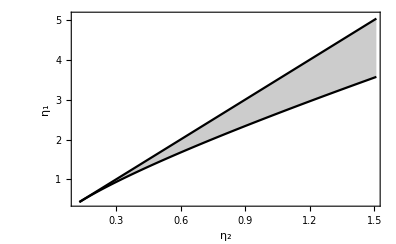

```mathematica
ListLinePlot[{Tab1,Tab2},PlotRange->{{Min[Tab1]-0.01,1.5},{Tab2[[1]][[2]]-0.01,5.1}},Filling->{1->{2}},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"η_1",None},{"η_2",None}},FrameTicks->All,RotateLabel->True,PlotStyle->{Black,Black},AxesOrigin->{0,0}]
```